Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.1 (Approssimazione di funzione con il suo sviluppo di Taylor).

### Testo dell’esercizio

Come sono approssimate le funzioni sin(x) e 1/(1+x^2) dai loro polinomi di Taylor di ordine crescente?

### Svolgimento

Il mio obiettivo è plottare su una griglia dei grafici con passo che aumenta tra le righe di f(x) contro il suo sviluppo in serie di Taylor (in 0). Cominciamo dicendo

```mathematica
g[x_]:= 1/(1+x^2)
```

Ora necessito che lo step tra i grafici di una riga sia n quindi automatizzo la creazione delle righe per una funzione generica in un intervallo fissato [-10,10] per limitare le variabili. diamo anche una lunghezza di 4 
fissata alle righe e ricordandoci di quale ordine stiamo facendo il grafico

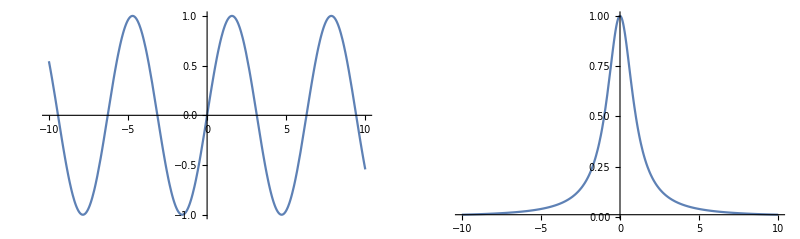

```mathematica
GraphicsRow[{Plot[Sin[x],{x,-10,10}],Plot[g[x],{x,-10,10},PlotRange->Full]}]
```

Possiamo notare che possiamo tenere un PlotRange tra -1 ed 1 senza separarle , per sicurezza facciamo 1.5 valà

```mathematica
Rows[f_,x_,start_,step_]:=Table[Plot[{f[x] , Series[f[x],{x,0,k}]//Normal//Evaluate},{x,-10,10},PlotLabel->k,PlotRange->{-1.5,1.5}],{k,start,start+4 step,step}]
```

La funzione crea una table con il grafico di f(x) e quello della sua serie di Taylor al k-esimo ordine con k che varia, facendo 4 grafici per riga con step fissato

Creiamo una funzione che dia una matrice fatta di “Rows” dove lo step incrementi col numero di righe. ciò crea un problema nel calcolare con cosa far cominciare le righe.

```mathematica
Gridd[f_,x_,n_]:= Table[Rows[f,x,st[k],k],{k,1,n}]
```

lo start della riga 1 è 1, lo start della riga 2 è (1 + 4step(1)+step(1)), lo start della riga 3 è (start della riga 2 + 4step(2)+step(2)) viene in mente di definire ricorsivamente st[k], ricordandoci che step(k) = k per definizione

```mathematica
st[k_]:= st[k-1]+ 5k
```

```mathematica
st[1] := 1
```

Plottiamo e mettiamo in una tabella

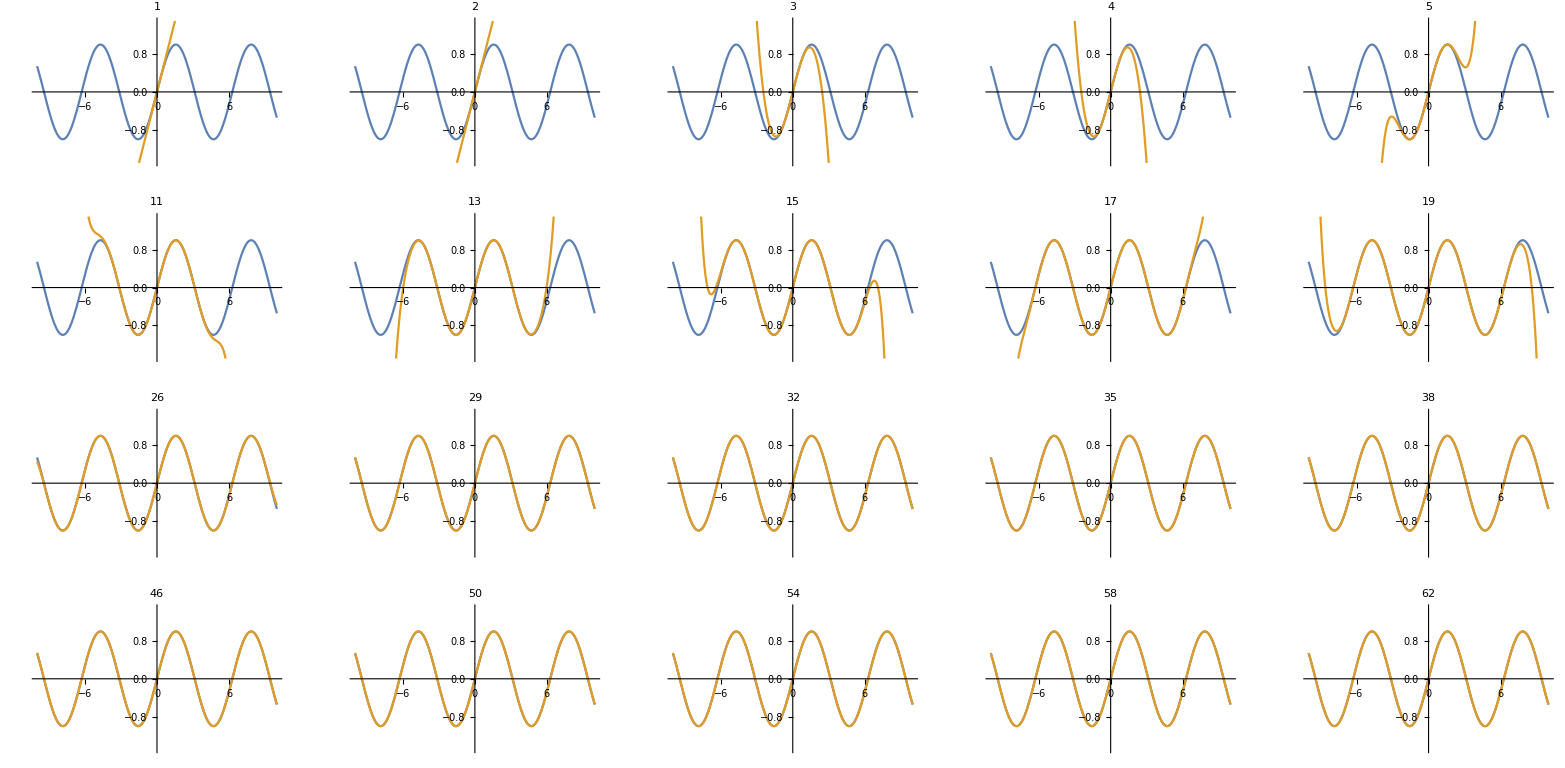

```mathematica
GraphicsGrid[Gridd[Sin,x,4],ImageSize->Full]
```

Proviamo a fare lo stesso con g

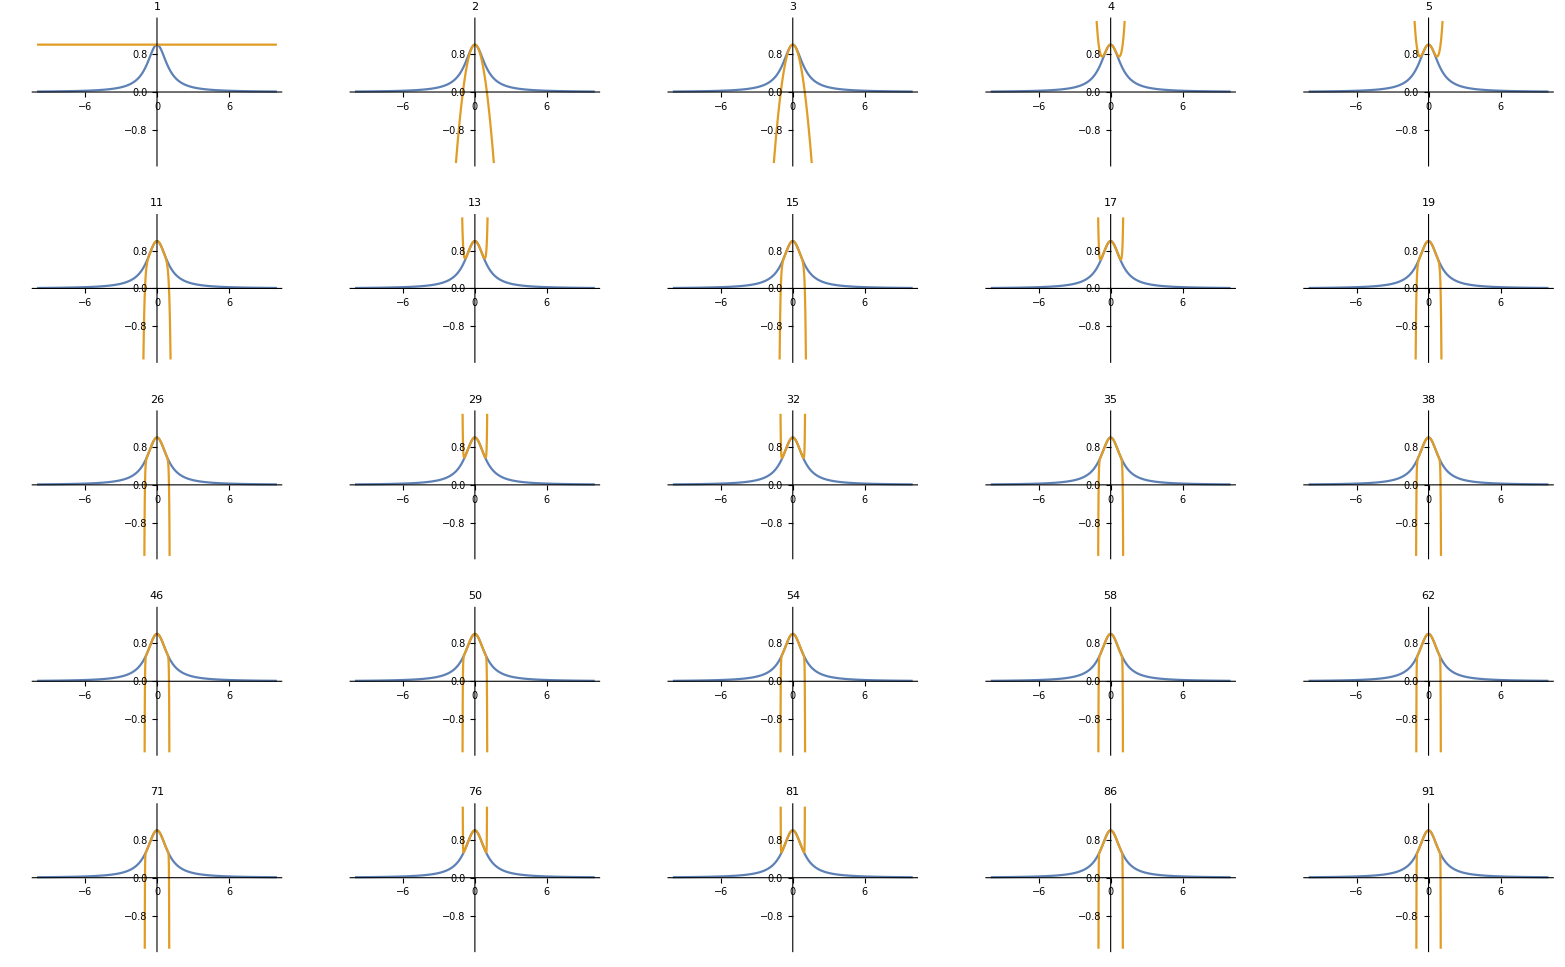

```mathematica
GraphicsGrid[Gridd[g,x,5],ImageSize->Full]
```

Si notano subito spiccate differenze sulla convergenza tra Sin(x) e 1/(1+x^2), la serie di Sin(x), pur essendo entrambe analitiche. 
Lo sviluppo di Sin(x) si “appiccica” alla funzione nell’intervallo [-10,10] in meno di 30 iterazioni, quello di 1/(1+x^2) in 100 non è arrivato a metà
Mi vien da chiedermi quanto sia veloce l’approssimazione, posso provare a farlo plottando n sul il primo x>0 per cui lo sviluppo di ordine n è diverso dalla funzione (entrambe le funzioni hanno simmetrie comode)
scritto matematicamente F(n) = inf(x>0 : |f(x)-s.taylor ord. n f(x)|>0 ), scritto mathematicamente

```mathematica
dst[f_,x_,n_] := Abs[f[x]-Evaluate@Normal[Series[f[x],{x,0,n}]]]
```

Forse c’è un metodo migliore ma si può risolvere numericamente mettendogli un numero “piccolo”>0, forse c’è un metodo migliore

```mathematica
ConvSin=FindRoot[dst[Sin,x,#]==0.01,{x,#-2}]&
```

```mathematica
Convg=FindRoot[dst[g,x,#]==0.01,{x,#/55}]&
```

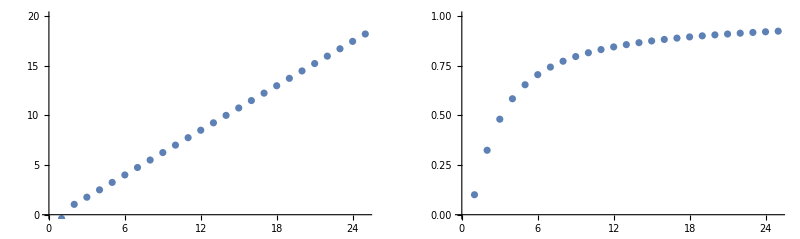

```mathematica
GraphicsRow [{ListPlot[x/.ConvSin/@Range[1,50,2],PlotRange->{0,20}],ListPlot[x/.Convg/@Range[1,50,2],PlotRange->{0,1}]}]
```

Sembra una convergenza lineare la prima e logaritmica la seconda.
possiamo vedere come nel medesimo numero di passi il primo sviluppo di Taylor stia “incollato” alla funzione fino a circa x = 20, il secondo circa a x = 1

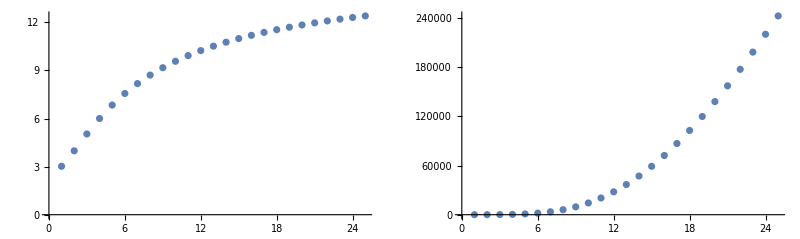

```mathematica
GraphicsRow[{ListPlot[Exp@Exp[x/.Convg/@Range[1,50,2]]],ListPlot[Exp@Exp@Exp[x/.Convg/@Range[1,50,2]]]}]
```

Tuttavia se plottiamo e^(f(x)) è concava (=> sublineare), così come e^(e^(f(x))), tuttavia e^(e^(e^(f(x))))diventa convessa (=> superlineare), credo si può concludere che la convergenza dell’approssimazione di taylor di 1/(1+x^2) alla funzione sia compresa tra log(log(x)) e log(log(log(x)))

## Esercizio 1.2 (Algebra e coreografie).

### Testo dell’esercizio

Le tre radici del polinomio x^3+bx+c dipendono dai coefficienti b e c e sono generalmente complesse (e distinte, ma per speciali valori di b e c una o tutte possono essere reali e due o tutte possono coincidere).
Per ogni scelta di b e c, le radici sono dunque tre (o due o uno) punti nel piano complesso.
Se si fa muovere il punto (b,c)∈ℝ^2 lungo una curva Γ in ℝ^2, le radici si muovono lungo tre curve (che possono avere delle intersezioni) nel piano complesso ℂ. Si chiede di generare un filmato che mostra, affiancati, il moto del punto (b,c)∈ℝ^2 lungo una curva e il corrispondente moto (o danza) delle radici in ℂ.

#### Svolgimento

Allora, cominciamo dando un nome al nostro polinomio, equivalentemente assegnando una funzione che manda la terna (b,c,x) nel polinomio di terzo grado sopra

```mathematica
P[b_,c_,x_]:= x^3+b x + c
```

Ora due funzioni che ci diano le radici ed il plot su ℝ^2 delle stesse

```mathematica
Rads[a_,b_]:= x/.NSolve[P[a,b,x]]
```

```mathematica
C2R2[z_]:= {Re[z],Im[z]}
```

## Esercizio 1.3 (Teorema dei numeri primi).

### Testo dell’esercizio

Il teorema dei numeri primi afferma che le funzioni π(n), n/(log(n)), li(n) sono asintotiche per n→∞. Investigare numericamente quest’affermazione.

### Svolgimento

Ricorrendo al risolutore di limiti interno a Mathematica, possiamo vedere che le tre funzioni sono asintotiche per n→∞.

```mathematica
{
Limit[PrimePi[n]/(n/Log[n]),n->∞],
Limit[PrimePi[n]/LogIntegral[n],n->∞]
}
```

Ciò non significa che il modulo della differenza tra due delle funzioni in esame sia infinitesimo. Come si vede nel grafico seguente, la differenza in valore assoluto tra π(n) e n/(log(n)) è tendenzialmente crescente. Dal grafico, però, non è chiaro se esista α∈ℝ tale che n^α sia asintotico a |π(n)-n/(log(n))|.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-x/Log[x]],
x^α
},
{x,10^k,10^(k+3)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-x/Log[x]]],TraditionalForm[x^α]},Ticks->{N@(10^Range[k,k+3]),Automatic}(*La N impedisce che i numeri sotto i tick compaiano per esteso anche quando troppo lunghi.*)
],
{k,Range[9]},(*Questa sintassi permette di ottenere un controllo a tendina anziché a slider.*)
{α,0.1,1}
]
```

Confrontando π(n) con li(n), seppur con oscillazioni più pronunciate, si ottiene ugualmente che la differenza in valore assoluto tra le due funzioni non è infinitesima, ma tendente a ∞ per n→∞. Anche in questo caso non è facile individuare “ad occhio” l’esponente β tale che n^β sia asintotico a |π(n)-li(n)|.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-LogIntegral[x]],
x^β
},
{x,10^k,10^(k+2)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-LogIntegral[x]]],TraditionalForm[x^β]},Ticks->{N@(10^Range[k,k+2]),Automatic}
],
{k,Range[10]},
{β,0.3,.45}
]
```

Qui comincia la parte interessante

```mathematica
Manipulate[
LogLogPlot[PrimePi[x]/(x/Log[x]),
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotRange->{.99,1.3}
],
{k,Range[0,9]}
]
```

```mathematica
Manipulate[
LogLogPlot[PrimePi[x]/LogIntegral[x],
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotRange->{0.6,1.0001}
],
{k,Range[9]}
]
```

L’evidenza richiesta

```mathematica
Manipulate[
LogLogPlot[PrimePi[x]/(x/Log[x])-1,
{x,10^k,10^(k+3)},
PlotStyle->Blue,
Ticks->{N@(10^Range[k,k+3]),Automatic},PlotRange->{0.01,0.3}
],
{k,Range[0,9]}
]
```

```mathematica
Manipulate[
LogLogPlot[Abs[PrimePi[x]/LogIntegral[x]-1],
{x,10^k,10^(k+3)},
PlotStyle->Blue,
Ticks->{N@(10^Range[k,k+3]),Automatic}
],
{k,Range[9]}
]
```

## Esercizio 1.4 (Catenaria).

### Testo dell’esercizio

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata catenaria, di equazioni parametriche

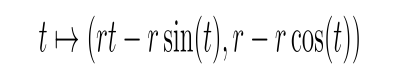

Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che rotola, il punto P su di essa, e la curva descritta da P nel piano.

### Svolgimento